# Happy End Problem

### Author

Eric W. Weisstein
August 12, 2026

This notebook downloaded from https://mathworld.wolfram.com/notebooks/ComputationalGeometry/HappyEndProblem.nb.

For more information, see Eric's MathWorld entry https://mathworld.wolfram.com/HappyEndProblem.html.

©2026 Wolfram Research, Inc. except for portions noted otherwise

## Computational

```mathematica
<<DiscreteMath`ComputationalGeometry`
<<DiscreteMath`Combinatorica`
```

```mathematica
ConvexNGon[l_List,n_]:=Module[{s=Select[#[[ConvexHull[#]]]&/@KSubsets[l,n],Length[#]==n&,1]},
If[s=={},{},s[[1]]]
]

ClosedLine[l_]:=Line[Append[l,First[l]]]

NGon[l_,n_]:=Module[{c=ConvexNGon[l,n]},
If[c=={},{},ClosedLine[c]]
]
```

### Triangle

```mathematica
p=Table[Random[Real],{5},{3},{2}]
```

{{{0.898267,0.484221},{0.719938,0.653005},{0.870774,0.617118}},{{0.262849,0.778953},{0.117787,0.55409},{0.569413,0.0636896}},{{0.81604,0.00737995},{0.00280351,0.831251},{0.169235,0.828384}},{{0.894232,0.313866},{0.722286,0.930477},{0.678055,0.935346}},{{0.824019,0.446256},{0.958118,0.282341},{0.953246,0.829138}}}

```mathematica
Union[Length/@(ConvexNGon[#,3]&/@p)]
```

{3}

```mathematica
Show[GraphicsArray[
Graphics[
{
PointSize[.08],
Point/@#,
NGon[#,3]
},
AspectRatio->Automatic,PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None]&/@p]]
```

⁃GraphicsArray⁃

### Square

#### 4 Points

```mathematica
p4=Table[Random[Real],{10},{4},{2}]
```

{{{0.10141,0.839115},{0.184596,0.635342},{0.506386,0.302394},{0.483479,0.595412}},{{0.544442,0.514072},{0.902068,0.198861},{0.242257,0.213369},{0.793705,0.387086}},{{0.222215,0.165175},{0.832228,0.165095},{0.538189,0.0447509},{0.907808,0.91906}},{{0.436779,0.205636},{0.723212,0.283717},{0.930393,0.903242},{0.239732,0.688305}},{{0.385952,0.389169},{0.337664,0.489444},{0.143695,0.175801},{0.54396,0.102358}},{{0.92148,0.0106254},{0.711731,0.937263},{0.383291,0.965874},{0.803923,0.0182033}},{{0.946511,0.760239},{0.0807113,0.734486},{0.016118,0.856997},{0.840979,0.0461806}},{{0.630166,0.467828},{0.503314,0.556737},{0.486471,0.292028},{0.959355,0.454379}},{{0.564992,0.281402},{0.247623,0.517116},{0.181701,0.315528},{0.4437,0.498912}},{{0.23519,0.555289},{0.362989,0.764426},{0.219072,0.698292},{0.52201,0.718246}}}

```mathematica
Union[Length/@(ConvexNGon[#,4]&/@p4)]
```

{0,4}

```mathematica
Show[GraphicsArray[
Partition[Graphics[
{
PointSize[.08],
Point/@#,
NGon[#,4]
},
AspectRatio->Automatic,PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None]&/@p4,5]]]
```

⁃GraphicsArray⁃

#### 5 Points

```mathematica
p5=Table[Random[Real],{10},{5},{2}]
```

{{{0.931691,0.327006},{0.935785,0.419065},{0.494536,0.88684},{0.259219,0.946807},{0.839935,0.53405}},{{0.632032,0.802956},{0.771482,0.134368},{0.834007,0.455515},{0.994252,0.64145},{0.127943,0.580917}},{{0.525897,0.866416},{0.240965,0.902513},{0.594206,0.539409},{0.30518,0.483448},{0.09967,0.652569}},{{0.0459613,0.536641},{0.259735,0.118519},{0.413929,0.733685},{0.488254,0.984151},{0.579922,0.27817}},{{0.494001,0.342701},{0.45198,0.697253},{0.968105,0.476285},{0.211015,0.79474},{0.373899,0.936876}},{{0.905835,0.311291},{0.274228,0.284307},{0.859874,0.77465},{0.0144932,0.165788},{0.445945,0.0409649}},{{0.52624,0.181637},{0.866022,0.762795},{0.0322384,0.838936},{0.414043,0.0655424},{0.0641339,0.36265}},{{0.203028,0.270803},{0.690235,0.425775},{0.297193,0.959511},{0.416007,0.141468},{0.437319,0.184861}},{{0.401514,0.975681},{0.991375,0.143896},{0.875274,0.794044},{0.125353,0.381101},{0.843036,0.955108}},{{0.71131,0.315559},{0.778902,0.592458},{0.508282,0.044756},{0.0886663,0.166683},{0.211089,0.0852447}}}

```mathematica
Union[Length/@(ConvexNGon[#,4]&/@p5)]
```

{4}

```mathematica
Show[GraphicsArray[
Partition[Graphics[
{
PointSize[.08],
Point/@#,
NGon[#,4]
},
AspectRatio->Automatic,PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None]&/@p5,5]]]
```

⁃GraphicsArray⁃

### Pentagon

#### 8 Points

```mathematica
p8=Table[Random[Real],{10},{8},{2}]
```

{{{0.412158,0.970847},{0.971797,0.653261},{0.849935,0.357114},{0.972314,0.998025},{0.538365,0.345443},{0.277357,0.455394},{0.431361,0.556607},{0.307406,0.0216693}},{{0.437291,0.0122526},{0.150094,0.686047},{0.977835,0.577583},{0.359956,0.57548},{0.565677,0.606736},{0.388159,0.92222},{0.715742,0.249622},{0.415845,0.924195}},{{0.177377,0.904179},{0.138488,0.468801},{0.746016,0.347573},{0.831082,0.447132},{0.308725,0.33532},{0.680988,0.761085},{0.330889,0.757737},{0.321032,0.185604}},{{0.765212,0.151001},{0.932873,0.263385},{0.0494707,0.901379},{0.517028,0.33919},{0.872094,0.9972},{0.37854,0.870389},{0.126078,0.649627},{0.547458,0.423257}},{{0.817353,0.314307},{0.86647,0.662173},{0.486464,0.55657},{0.545439,0.476568},{0.721251,0.405569},{0.612566,0.213184},{0.671781,0.50419},{0.0955383,0.873994}},{{0.799687,0.50699},{0.716999,0.00360465},{0.673609,0.857363},{0.169541,0.580347},{0.856256,0.543055},{0.303071,0.918175},{0.369792,0.986485},{0.757632,0.441607}},{{0.648541,0.580916},{0.145066,0.228423},{0.97676,0.0767259},{0.0495276,0.354429},{0.177073,0.569736},{0.332529,0.350825},{0.503464,0.712373},{0.162988,0.770477}},{{0.647207,0.169317},{0.859917,0.852302},{0.277415,0.182832},{0.102285,0.410696},{0.628874,0.601916},{0.957219,0.182273},{0.652114,0.52519},{0.907692,0.827843}},{{0.475041,0.955455},{0.575163,0.477019},{0.971577,0.243082},{0.412175,0.706541},{0.32437,0.0737645},{0.552258,0.854239},{0.0469547,0.890932},{0.449972,0.443544}},{{0.418081,0.289016},{0.492753,0.261271},{0.765967,0.763826},{0.585061,0.433427},{0.290926,0.808371},{0.0098982,0.956409},{0.319349,0.565289},{0.597723,0.249867}}}

```mathematica
Union[Length/@(ConvexNGon[#,5]&/@p8)]
```

{0,5}

```mathematica
Show[GraphicsArray[
Partition[Graphics[
{
PointSize[.08],
Point/@#,
NGon[#,5]
},
AspectRatio->Automatic,PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None]&/@p8,5]]]
```

⁃GraphicsArray⁃

#### 9 Points

```mathematica
p9=Table[Random[Real],{100},{9},{2}];
```

```mathematica
Union[Length/@(ConvexNGon[#,5]&/@p9)]//Timing
```

{12.67 Second,{5}}

### Hexagons

```mathematica
p=Table[Random[Real],{100},{30},{2}];
```

```mathematica
i=0;
While[l=Length[ConvexNGon[r=Table[Random[Real],{9},{2}],6]]>0,i++;
If[Mod[i,10]==0,Print[i,"..."]
]];
{i,r,ConvexNGon[r,6]}
```

{7,{{0.544593,0.56834},{0.282622,0.763949},{0.606376,0.242303},{0.533673,0.000350439},{0.722853,0.904031},{0.00984797,0.926969},{0.0839587,0.852759},{0.529125,0.671452},{0.85365,0.0888226}},{}}

```mathematica
i=0;
While[l=Length[ConvexNGon[r=Table[Random[Real],{10},{2}],6]]>0,i++;
If[Mod[i,10]==0,Print[i,"..."]
]];
{i,r,ConvexNGon[r,6]}
```

10...

{10,{{0.93329,0.297627},{0.877949,0.497724},{0.625728,0.596887},{0.338524,0.33849},{0.593514,0.406649},{0.559693,0.232912},{0.130017,0.135801},{0.725126,0.78087},{0.695283,0.53883},{0.0365407,0.187587}},{}}

```mathematica
i=0;
While[l=Length[ConvexNGon[r=Table[Random[Real],{11},{2}],6]]>0,i++;
If[Mod[i,10]==0,Print[i,"..."]
]];
{i,r,ConvexNGon[r,6]}
```

830...

840...

850...

860...

870...

{878,{{0.784859,0.58826},{0.787067,0.493128},{0.346887,0.32467},{0.432607,0.670366},{0.835043,0.349584},{0.286527,0.0890499},{0.496651,0.56164},{0.850291,0.791956},{0.542885,0.504643},{0.0345573,0.865593},{0.301658,0.696466}},{}}

```mathematica
p={{0.7848594046731805,0.5882600968568017},{0.7870669047148386,0.49312823419061813},{0.3468871016811131,0.324669627515676},{0.4326068692173522,0.670365965383893},{0.8350430353588773,0.3495840886962882},{0.28652693461562134,0.08904993071347599},{0.4966514482762856,0.561640009755739},{0.8502911421386248,0.7919564903954044},{0.5428853133116156,0.5046432847692016},{0.034557335898123966,0.8655929252371125},{0.3016578387177457,0.6964659969105412}};
```

```mathematica
Or@@CollinearQ/@KSubsets[Point/@p,3]
```

False

```mathematica
Or@@CollinearQ/@KSubsets[Point/@Rationalize[p,0],3]
```

False

```mathematica
ConvexNGon[Rationalize[p,0],6]
```

{}

```mathematica
Show[Graphics[
{
PointSize[.08],
Point/@p,
NGon[p,6]
},
AspectRatio->Automatic,PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None]]
```

⁃Graphics⁃

```mathematica
i=0;
While[l=Length[ConvexNGon[r=Table[Random[Real],{12},{2}],6]]>0,i++;
If[Mod[i,10]==0,Print[i,"..."]
]];
{i,r,ConvexNGon[r,6]}
```

{6371,{{0.875619,0.367026},{0.923776,0.825757},{0.719194,0.969746},{0.655999,0.912496},{0.354966,0.829543},{0.704779,0.661158},{0.184303,0.246788},{0.141283,0.85477},{0.706302,0.769899},{0.0165236,0.111496},{0.223195,0.827833},{0.217896,0.285193}},{}}

```mathematica
t=AbsoluteTime[];
i=0;
While[l=Length[ConvexNGon[r=Table[Random[Real],{13},{2}],6]]>0,i++;
If[Mod[i,10]==0,Print[i,"..."]
]];
{AbsoluteTime[]-t,i,r,ConvexNGon[r,6]}
```

32280...

```mathematica
t=AbsoluteTime[];
i=0;
While[l=Length[ConvexNGon[r=Table[Random[Real],{14},{2}],6]]>0,i++;
If[Mod[i,10]==0,Print[i,"..."]
]];
{AbsoluteTime[]-t,i,r,ConvexNGon[r,6]}
```

10610...

$Aborted

30838 Seconds...

## Values

3, 5, 9, ≥13 (experimental) / ≥ 17 (theoretical)

## Bounds

### Lower Bounds

```mathematica
Table[2^(n-2)+1,{n,6}]
```

{3/2,2,3,5,9,17}

### Upper Bounds

```mathematica
f[1,n_]:=f[2,n]+1
f[2,n_]:=Binomial[2n-4,n-2]
f[3,n_]:=Binomial[2n-4,n-2]+7-2n
f[4,n_]:=Binomial[2n-5,n-2]+2
```

```mathematica
Table[f[k,n],{k,4},{n,10}]//ColumnForm
```

{1,2,3,7,21,71,253,925,3433,12871}
{0,1,2,6,20,70,252,924,3432,12870}
{5,4,3,5,17,65,245,915,3421,12857}
{2,3,3,5,12,37,128,464,1718,6437}

## Erdos-Szekeres Point Sets

These point sets contain no convex 5-gon, 6-gon, and 7-gon, respectively. The 32-point set is the integer-coordinate example of Duque, Fabila-Monroy, and Hidalgo-Toscano (2018).

```mathematica
pts8={{18,342},{342,342},{18,18},{126,261},{261,234},{234,99},{171001/500,18},{99,126}};pts16={{19,305},{254,479},{490,304},{401,25},{110,22},{25091/100,453/2},{5851/50,7413/50},{10128/25,6079/50},{27243/100,17993/50},{2298/25,25673/100},{41349/100,18027/100},{5716/25,14299/50},{6407/25,40637/100},{11617/100,21629/100},{24537/100,6633/25},{10188/25,818/5}};pts32={{0,0},{84,-9},{85,-9},{86,-8},{89,-4},{90,-2},{152,-41},{153,-40},{154,-40},{159,-32},{160,-32},{161,-31},{162,-24},{163,-24},{164,-23},{167,-19},{198,-103},{201,-99},{202,-98},{203,-98},{204,-91},{205,-90},{206,-90},{211,-82},{212,-82},{213,-81},{222,-195},{223,-193},{226,-189},{227,-188},{228,-188},{230,-310}};
```

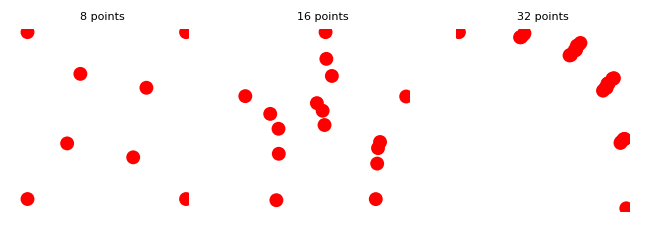

```mathematica
GraphicsRow[Function[pts,ListPlot[pts,PlotStyle->Directive[Red,PointSize[1/40]],AspectRatio->1,Axes->False,PlotLabel->Style[Row[{Length[pts]," points"}],Directive[14,FontFamily->"Times"]]]]/@{pts8,pts16,pts32},Dividers->All]
```